```mathematica
SetDirectory["/home/ethan/spring20/comphys/week3/quiz/"]
```

/home/ethan/spring20/comphys/week3/quiz

```mathematica
res = ReadList["data.txt",{Number,Number} ]
```

{{1.,1.},{1.01,0.995037},{1.02,0.990148},{1.03,0.985329},{1.04,0.980581},{1.05,0.9759},{1.06,0.971286},{1.07,0.966736},{1.08,0.96225},{1.09,0.957826},{1.1,0.953463},{1.11,0.949158},{1.12,0.944911},{1.13,0.940721},{1.14,0.936586},{1.15,0.932505},{1.16,0.928477},{1.17,0.9245},{1.18,0.920575},{1.19,0.916698},{1.2,0.912871},{1.21,0.909091},{1.22,0.905357},{1.23,0.90167},{1.24,0.898027},{1.25,0.894427},{1.26,0.890871},{1.27,0.887357},{1.28,0.883883},{1.29,0.880451},{1.3,0.877058},{1.31,0.873704},{1.32,0.870388},{1.33,0.86711},{1.34,0.863868},{1.35,0.860663},{1.36,0.857493},{1.37,0.854358},{1.38,0.851257},{1.39,0.848189},{1.4,0.845154},{1.41,0.842152},{1.42,0.839181},{1.43,0.836242},{1.44,0.833333},{1.45,0.830455},{1.46,0.827606},{1.47,0.824786},{1.48,0.821995},{1.49,0.819232},{1.5,0.816497},{1.51,0.813788},{1.52,0.811107},{1.53,0.808452},{1.54,0.805823},{1.55,0.803219},{1.56,0.800641},{1.57,0.798087},{1.58,0.795557},{1.59,0.793052},{1.6,0.790569},{1.61,0.78811},{1.62,0.785674},{1.63,0.78326},{1.64,0.780869},{1.65,0.778499},{1.66,0.776151},{1.67,0.773823},{1.68,0.771517},{1.69,0.769231},{1.7,0.766965},{1.71,0.764719},{1.72,0.762493},{1.73,0.760286},{1.74,0.758098},{1.75,0.755929},{1.76,0.753778},{1.77,0.751646},{1.78,0.749532},{1.79,0.747435},{1.8,0.745356},{1.81,0.743294},{1.82,0.741249},{1.83,0.739221},{1.84,0.73721},{1.85,0.735215},{1.86,0.733236},{1.87,0.731272},{1.88,0.729325},{1.89,0.727393},{1.9,0.725476},{1.91,0.723575},{1.92,0.721688},{1.93,0.719816},{1.94,0.717958},{1.95,0.716115},{1.96,0.714286},{1.97,0.71247},{1.98,0.710669},{1.99,0.708881},{2.,0.707107}}

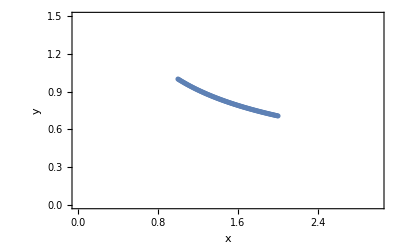

```mathematica
ListPlot[res, Frame->True, FrameLabel-> {"x","y"}, PlotRange->{{0,3},{0,1.5}}]
```

```mathematica
SetDirectory["/home/ethan/spring20/comphys/week3/rooney/"]
```

/home/ethan/spring20/comphys/week3/rooney

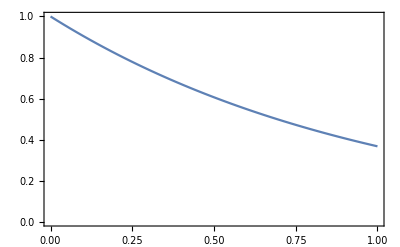

Part::partw: Part -1 of {} does not exist.

```mathematica
data = ReadList["!./differential 0.00001 100000", {Number, Number}];
Show[ListPlot[data, Frame->True, PlotRange->{{-0.1,1.1},{0, 1.1}}], Plot[Exp[-t],{t,0,1}]]
(data[[-1,2]]-Exp[-1])/Exp[-1]
```

```mathematica
ⅇ (-1/ⅇ+{}⟦-1,2⟧)-Graphics-
```

```mathematica
0.000016792307637563774
```

0.0000167923

```mathematica
res[n_, i_] := ReadList[ "!./integral2 1, 6.28318530717958647692528676655900576901, 0, " <>ToString[n]<> ", " <>ToString[i] <> " ", {Number, Number, Number, Number, Number, Number, Number}];
```

SetDelayed::write: Tag List in {{1.,1.},{1.01,0.995037},{1.02,0.990148},{1.03,0.985329},{1.04,0.980581},{1.05,0.9759},{1.06,0.971286},{1.07,0.966736},{1.08,0.96225},{1.09,0.957826},{1.1,0.953463},«30»,{1.41,0.842152},{1.42,0.839181},{1.43,0.836242},{1.44,0.833333},{1.45,0.830455},{1.46,0.827606},{1.47,0.824786},{1.48,0.821995},{1.49,0.819232},«51»}[n_,i_] is Protected.

```mathematica
data = res[0.01, 1]
ListPlot[{ data[[All,{1,2}]],
		data[[All,{1,3}]],
		data[[All, {1,4}]],
		data[[All, {1,5}]],
		data[[All, {1,6}]]},
		PlotLegends->{"v_x", "v_y", "x", "y", "Energy", "r"},
		Joined->True]
```

SetDelayed::write: Tag List in {{1.,1.},{1.01,0.995037},{1.02,0.990148},{1.03,0.985329},{1.04,0.980581},{1.05,0.9759},{1.06,0.971286},{1.07,0.966736},{1.08,0.96225},{1.09,0.957826},{1.1,0.953463},«30»,{1.41,0.842152},{1.42,0.839181},{1.43,0.836242},{1.44,0.833333},{1.45,0.830455},{1.46,0.827606},{1.47,0.824786},{1.48,0.821995},{1.49,0.819232},«51»}[n_,i_] is Protected.

{{1.,1.},{1.01,0.995037},{1.02,0.990148},{1.03,0.985329},{1.04,0.980581},{1.05,0.9759},{1.06,0.971286},{1.07,0.966736},{1.08,0.96225},{1.09,0.957826},{1.1,0.953463},{1.11,0.949158},{1.12,0.944911},{1.13,0.940721},{1.14,0.936586},{1.15,0.932505},{1.16,0.928477},{1.17,0.9245},{1.18,0.920575},{1.19,0.916698},{1.2,0.912871},{1.21,0.909091},{1.22,0.905357},{1.23,0.90167},{1.24,0.898027},{1.25,0.894427},{1.26,0.890871},{1.27,0.887357},{1.28,0.883883},{1.29,0.880451},{1.3,0.877058},{1.31,0.873704},{1.32,0.870388},{1.33,0.86711},{1.34,0.863868},{1.35,0.860663},{1.36,0.857493},{1.37,0.854358},{1.38,0.851257},{1.39,0.848189},{1.4,0.845154},{1.41,0.842152},{1.42,0.839181},{1.43,0.836242},{1.44,0.833333},{1.45,0.830455},{1.46,0.827606},{1.47,0.824786},{1.48,0.821995},{1.49,0.819232},{1.5,0.816497},{1.51,0.813788},{1.52,0.811107},{1.53,0.808452},{1.54,0.805823},{1.55,0.803219},{1.56,0.800641},{1.57,0.798087},{1.58,0.795557},{1.59,0.793052},{1.6,0.790569},{1.61,0.78811},{1.62,0.785674},{1.63,0.78326},{1.64,0.780869},{1.65,0.778499},{1.66,0.776151},{1.67,0.773823},{1.68,0.771517},{1.69,0.769231},{1.7,0.766965},{1.71,0.764719},{1.72,0.762493},{1.73,0.760286},{1.74,0.758098},{1.75,0.755929},{1.76,0.753778},{1.77,0.751646},{1.78,0.749532},{1.79,0.747435},{1.8,0.745356},{1.81,0.743294},{1.82,0.741249},{1.83,0.739221},{1.84,0.73721},{1.85,0.735215},{1.86,0.733236},{1.87,0.731272},{1.88,0.729325},{1.89,0.727393},{1.9,0.725476},{1.91,0.723575},{1.92,0.721688},{1.93,0.719816},{1.94,0.717958},{1.95,0.716115},{1.96,0.714286},{1.97,0.71247},{1.98,0.710669},{1.99,0.708881},{2.,0.707107}}[0.01,1]

Part::partd: Part specification {{1.,1.},{1.01,0.995037},{1.02,0.990148},{1.03,0.985329},{1.04,0.980581},{1.05,0.9759},{1.06,0.971286},{1.07,0.966736},{1.08,0.96225},{1.09,0.957826},{1.1,0.953463},«30»,{1.41,0.842152},{1.42,0.839181},{1.43,0.836242},{1.44,0.833333},{1.45,0.830455},{1.46,0.827606},{1.47,0.824786},{1.48,0.821995},{1.49,0.819232},«51»}[«5»,1]⟦«1»⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-